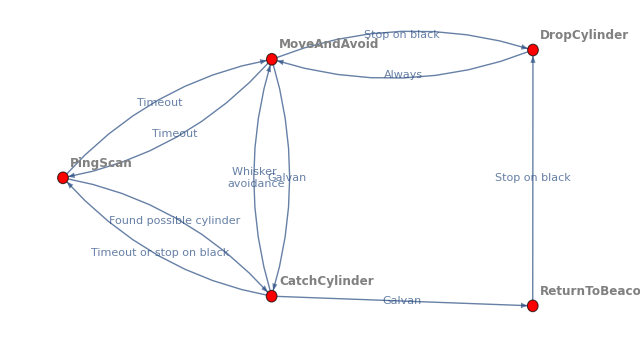

```mathematica
g=Graph[{
MoveAndAvoid->PingScan,MoveAndAvoid->CatchCylinder,MoveAndAvoid->DropCylinder,
PingScan->MoveAndAvoid,PingScan->CatchCylinder,
CatchCylinder->MoveAndAvoid,CatchCylinder->PingScan,CatchCylinder->ReturnToBeacon,
ReturnToBeacon->DropCylinder,
DropCylinder->MoveAndAvoid
},VertexLabels->"Name",EdgeLabels->{
MoveAndAvoid->PingScan->"Timeout",
MoveAndAvoid->CatchCylinder->"Galvan",
MoveAndAvoid->DropCylinder->"Stop on black",
PingScan->MoveAndAvoid->"Timeout",
PingScan->CatchCylinder->"Found possible cylinder",
CatchCylinder->MoveAndAvoid->"Whisker \navoidance",
CatchCylinder->PingScan->"Timeout or stop on black",
CatchCylinder->ReturnToBeacon->"Galvan",
ReturnToBeacon->DropCylinder->"Stop on black",
DropCylinder->MoveAndAvoid->"Always"
},VertexStyle->Red,VertexLabelStyle->Directive[Gray,Bold,12]]
```